```mathematica
Quit[]
```

## 1. Multiplets & Potential

### 1.1 Fields and Multiplets

```mathematica
(* Compex eigenstates of unbroken U(1)_e.m. *)
S={πp, Kp, πm , Km,     π0, K0, Kb0, η, ηp,     ap, Hp, am, Hm,     a0, H0, Hb0, f, σ} ;
(* Conjugated states: πp^*=πm etc *)
Sc={πm, Km, πp , Kp,     π0, Kb0, K0, η, ηp,     am, Hm, ap, Hp,     a0, Hb0, H0, f, σ} ;
(* VEVs for chiral (C) and Electroweak (EW) symmetry breaking *)
SvacC={πp->0, π0->0, πm->0, Kp->0, K0->0, Kb0->0, Km->0, η->0, ηp->0, ap->0, a0->0, am->0, Hp->0, H0->0, Hb0->0, Hm->0, f->0, σ->u} ;
SvacEW={πp->0, π0->0, πm->0, Kp->0, K0->0, Kb0->0, Km->0, η->0, ηp->0, ap->0, a0->0, am->0, Hp->0, H0->v/Sqrt[2], Hb0->v/Sqrt[2], Hm->0, f->0, σ->u} ;

(* Define Gauge states *)
SGauge = {π1,π3,K1,K3,η,ηp,     a1,a3,H1,H3,f,σ,     π2,K2,K4,     a2,H2,H4};
SvacCGauge={π1->0,π3->0,K1->0,K3->0,η->0,ηp->0,a1->0,a3->0,H1->0,H3->0,f->0,σ->u,π2->0,K2->0,K4->0, a2->0,H2->0,H4->0};
SvacEWGauge={π1->0,π3->0,K1->0,K3->0,η->0,ηp->0,a1->0,a3->0,H1->0,H3->v,f->0,σ->u,π2->0,K2->0,K4->0, a2->0,H2->0,H4->0};
$Assumptions={SGauge>0};
EW2Gauge = {πp->(π1+ⅈ π2)/(√2), π0->π3, πm->(π1-ⅈ π2)/(√2), Kp->(K1+ⅈ K2)/(√2), K0->(K3+ⅈ K4)/(√2), Kb0 ->(K3-ⅈ K4)/(√2), Km->(K1-ⅈ K2)/(√2), ap->(a1+ⅈ a2)/(√2), a0->a3, am->(a1-ⅈ a2)/(√2), Hp->(H1+ⅈ H2)/(√2), 
H0->(H3+ⅈ H4)/(√2), Hb0->(H3-ⅈ H4)/(√2), Hm->(H1-ⅈ H2)/(√2)};

(* Setting multiplets to zero. Useful for analysis *)
SingletsZ = {η->0, ηp->0,f->0, σ->0};
DoubletsZ = {Kp->0, K0->0, Kb0->0, Km->0, Hp->0, H0->0, Hb0->0, Hm->0};
TripletsZ = {πp->0, π0->0, πm->0, ap->0, a0->0, am->0};

(* Representation of the global chiral group SU3LxSU3R representation in terms 
of U(1)_e.m. eigenstates *)
Φ =1/(√2)({{a0/(√2)+f/(√6)+σ/(√3), ap, Hp}, {am, -a0/(√2)+f/(√6)+σ/(√3), H0}, {Hm, Hb0, -√(2/3)f+σ/(√3)}})-ⅈ/(√2)({{π0/(√2)+η/(√6)+ηp/(√3), πp, Kp}, {πm, -π0/(√2)+η/(√6)+ηp/(√3), K0}, {Km, Kb0, -√(2/3)η+ηp/(√3)}});
Φc =1/(√2)({{a0/(√2)+f/(√6)+σ/(√3), ap, Hp}, {am, -a0/(√2)+f/(√6)+σ/(√3), H0}, {Hm, Hb0, -√(2/3)f+σ/(√3)}})+ⅈ/(√2)({{π0/(√2)+η/(√6)+ηp/(√3), πp, Kp}, {πm, -π0/(√2)+η/(√6)+ηp/(√3), K0}, {Km, Kb0, -√(2/3)η+ηp/(√3)}});
ππ=({{π0/(√2), πp}, {πm, -π0/(√2)}});K=({{Kp}, {K0}});Kc=({{Km, Kb0}});a=({{a0/(√2), ap}, {am, -a0/(√2)}});H=({{Hp}, {H0}});Hc=({{Hm, Hb0}});Sing = {η,ηp,f,σ};
```

### 1.2 High-Energy Potential

```mathematica
ChiralV2D = ComplexExpand[-μ2∑_(i=1)^3 ∑_(j=1)^3 Φc[[i, j]]Φ[[j, i]]];
ChiralV3D = ComplexExpand[-2 √6 Λ3 Re[Det[Φ]]];
ChiralV4D = ComplexExpand[Subscript[λ, 1](∑_(i=1)^3 ∑_(j=1)^3 Φc[[i, j]]Φ[[j, i]])^2+3 Subscript[λ, 2](∑_(i=1)^3 ∑_(j=1)^3 ∑_(k=1)^3 ∑_(l=1)^3 Φc[[i, j]]Φ[[k, i]]Φc[[l, k]]Φ[[j, l]])];
ChiralV = ChiralV2D +ChiralV3D + ChiralV4D +σ θ +(H0+Hb0)/(√2)ω/.ω->0;
```

### 1.3 Low-Energy Potential

```mathematica
V2D = -(mS11 Sing[[1]]^2+mS22 Sing[[2]]^2+mS33 Sing[[3]]^2+mS44 Sing[[4]]^2   +   mS12 Sing[[1]]Sing[[2]]+mS34 Sing[[3]]Sing[[4]] +
	mT11 Tr[ππ.ππ]+mT22 Tr[a.a] +
	-mH11 Kc.K + -mH22 Hc.H ) [[1,1]];

V3D = (α113 Sing[[1]]^2 Sing[[3]]+α114 Sing[[1]]^2 Sing[[4]]+α123 Sing[[1]]Sing[[2]]Sing[[3]]+α124 Sing[[1]]Sing[[2]]Sing[[4]]   +   α223 Sing[[2]]^2 Sing[[3]]+α224 Sing[[2]]^2 Sing[[4]] +   
	α333 Sing[[3]]^3+α334 Sing[[3]]^2 Sing[[4]]+α344 Sing[[3]] Sing[[4]]^2+α444 Sing[[4]]^3 +
	β311 Sing[[3]]Tr[ππ.ππ]+β411 Sing[[4]]Tr[ππ.ππ]+β112 Sing[[1]]Tr[ππ.a]+β212 Sing[[2]]Tr[ππ.a] + β322 Sing[[3]]Tr[a.a]+β422 Sing[[4]]Tr[a.a] + 
	γ311 Sing[[3]] Kc.K+γ411 Sing[[4]] Kc.K   +   γ112 Sing[[1]]Kc.H+γ212 Sing[[2]]Kc.H+γ221 Sing[[2]]Hc.K+γ121 Sing[[1]]Hc.K   +   γ322 Sing[[3]]Hc.H+γ422 Sing[[4]]Hc.H + 
	Γ121 Kc.a.K+Γ112 Kc.ππ.H+Γ211 Hc.ππ.K+Γ222 Hc.a.H)[[1,1]];

V4D = Δ1111 Sing[[1]]^4+Δ1112 Sing[[1]]^3 Sing[[2]]+Δ1122 Sing[[1]]^2 Sing[[2]]^2+Δ1222 Sing[[1]] Sing[[2]]^3+Δ1133 Sing[[1]]^2 Sing[[3]]^2+Δ1134 Sing[[1]]^2 Sing[[3]]Sing[[4]]+Δ1144 Sing[[1]]^2 Sing[[4]]^2+
	Δ1233 Sing[[1]]Sing[[2]] Sing[[3]]^2+Δ1234 Sing[[1]]Sing[[2]]Sing[[3]]Sing[[4]]+Δ1244 Sing[[1]]Sing[[2]] Sing[[4]]^2 + 
	Δ2222 Sing[[2]]^4+Δ2233 Sing[[2]]^2 Sing[[3]]^2+Δ2234 Sing[[2]]^2 Sing[[3]]Sing[[4]]+Δ2244 Sing[[2]]^2 Sing[[4]]^2+
	Δ3333 Sing[[3]]^4+Δ3334 Sing[[3]]^3 Sing[[4]]+Δ3344 Sing[[3]]^2 Sing[[4]]^2+Δ3444 Sing[[3]] Sing[[4]]^3+Δ4444 Sing[[4]]^4 +

	η1111 Sing[[1]]^2 Tr[ππ.ππ]+η1211 Sing[[1]]Sing[[2]]Tr[ππ.ππ]+η2211 Sing[[2]]^2 Tr[ππ.ππ]+η3311 Sing[[3]]^2 Tr[ππ.ππ]+η3411 Sing[[3]]Sing[[4]]Tr[ππ.ππ]+η4411 Sing[[4]]^2 Tr[ππ.ππ] +
	η1312 Sing[[1]]Sing[[3]]Tr[ππ.a]+η1412 Sing[[1]]Sing[[4]]Tr[ππ.a]+η2312 Sing[[2]]Sing[[3]]Tr[ππ.a]+η2412 Sing[[2]]Sing[[4]]Tr[ππ.a] +
	η1122 Sing[[1]]^2 Tr[a.a]+η1222 Sing[[1]]Sing[[2]]Tr[a.a]+η2222 Sing[[2]]^2 Tr[a.a]+η3322 Sing[[3]]^2 Tr[a.a]+η3422 Sing[[3]]Sing[[4]]Tr[a.a]+η4422 Sing[[4]]^2 Tr[a.a] + 

	Π1111 Sing[[1]]^2 Kc.K+Π1211 Sing[[1]]Sing[[2]] Kc.K+Π2211 Sing[[2]]^2 Kc.K+Π3311 Sing[[3]]^2 Kc.K+Π3411 Sing[[3]]Sing[[4]] Kc.K+Π4411 Sing[[4]]^2 Kc.K+
	Π1312 Sing[[1]]Sing[[3]] Kc.H+Π1412 Sing[[1]]Sing[[4]] Kc.H+Π1321 Sing[[1]]Sing[[3]] Hc.K+Π1421 Sing[[1]]Sing[[4]] Hc.K + 
	Π2312 Sing[[2]]Sing[[3]] Kc.H+Π2412 Sing[[2]]Sing[[4]] Kc.H+Π2321 Sing[[2]]Sing[[3]] Hc.K+Π2421 Sing[[2]]Sing[[4]] Hc.K +
	Π1122 Sing[[1]]^2 Hc.H+Π1222 Sing[[1]]Sing[[2]] Hc.H+Π2222 Sing[[2]]^2 Hc.H+Π3322 Sing[[3]]^2 Hc.H+Π3422 Sing[[3]]Sing[[4]] Hc.H+Π4422 Sing[[4]]^2 Hc.H+

	Ζ1111 Sing[[1]]Kc.ππ.K+Ζ2111 Sing[[2]]Kc.ππ.K +Ζ3121 Sing[[3]]Kc.a.K+Ζ4121 Sing[[4]]Kc.a.K   +   Ζ3112 Sing[[3]]Kc.ππ.H+Ζ4112 Sing[[4]]Kc.ππ.H +Ζ1122 Sing[[1]]Kc.a.H+Ζ2122 Sing[[2]]Kc.a.H + 
	Ζ3211 Sing[[3]]Hc.ππ.K+Ζ4211 Sing[[4]]Hc.ππ.K +Ζ1221 Sing[[1]]Hc.a.K+Ζ2221 Sing[[2]]Hc.a.K   +   Ζ1212 Sing[[1]]Hc.ππ.H+Ζ2212 Sing[[2]]Hc.ππ.H +Ζ3222 Sing[[3]]Hc.a.H+Ζ4222 Sing[[4]]Hc.a.H + 

	(*Λ11 Tr[ππ.ππ]^2+Λ12 Tr[ππ.a]^2+Λ22 Tr[a.a]^2 + *)

	(*ρ1 Kc.K Tr[ππ.ππ]+ρ2 Kc.K Tr[a.a]+ρ3 Kc.H Tr[ππ.a]+ρ4 Hc.H Tr[ππ.a]+ρ5 Hc.H Tr[π.π] + ρ6 Hc.H Tr[a.a]+*)

	τ1 Kc.ππ.ππ.K+τ2 Kc.a.a.K+τ3 Kc.ππ.a.H+τ4 Kc.a.ππ.H+ τ5 Hc.ππ.a.K+τ6 Hc.a.ππ.K+τ7 Hc.ππ.ππ.H+τ8 Hc.a.a.H +

	Λ11 Tr[ππ.ππ.ππ.ππ]+Λ12 Tr[ππ.ππ.a.a]+Λ21 Tr[ππ.a.ππ.a]+Λ22 Tr[a.a.a.a] +

	υ11 (Kc.K)^2+υ12 (Kc.H)^2+υ21 (Hc.K)^2+υ22 (Hc.H)^2   +   ψ1 Kc.K.Hc.H+ψ2 Kc.H.Hc.K;

(* Full low-E potential *)
VEW=V4D+V3D+V2D + σ θ+(H0+Hb0)/(√2)ω/.ω->0;
```

### 1.4 Matching Parameters between Low-E and High-E Lagrangians

```mathematica
InputParam2D={mS11->μ2/2,mS22->μ2/2,mS33->μ2/2,mS44->μ2/2,mS12->0,mS34->0,mT11->μ2/2,mT22->μ2/2,mH11->-μ2,mH22->-μ2};

InputParam3D = {α113->-Λ3/(√2), α114->-Λ3/2, α123->-Λ3, α124->0, α223->0, α224->Λ3, α333->Λ3/(3√2), α334->Λ3/2 , α344->0, α444->-Λ3/3,
				β311->Λ3/(√2), β411->-Λ3/2,β112->√2Λ3,β212->-Λ3, β322->-Λ3/(√2), β422->Λ3/2,
				γ311->-Λ3/(√2),γ411->-Λ3,γ112->-Λ3/(√2),γ212->-Λ3,γ221->-Λ3,  γ121->-Λ3/(√2), γ311->-Λ3/(√2), γ322->Λ3/(√2), γ422->Λ3,
				Γ121-> √3Λ3 , Γ112->√3Λ3 , Γ211->√3Λ3, Γ222-> -√3Λ3 };

InputParam4D = {Δ1111->Subscript[λ, 1]/4+(3 Subscript[λ, 2])/8, Δ1112->-Subscript[λ, 2]/(√2), Δ1122->Subscript[λ, 1]/2+(3 Subscript[λ, 2])/2, Δ1222->0,Δ1133->Subscript[λ, 1]/2+(3 Subscript[λ, 2])/4,Δ1134->-Subscript[λ, 2]/(√2),Δ1144->Subscript[λ, 1]/2+Subscript[λ, 2]/2,
			 Δ1233->-Subscript[λ, 2]/(√2), Δ1234->2 Subscript[λ, 2], Δ1244->0, Δ2222->(Subscript[λ, 1]+ Subscript[λ, 2])/4, Δ2233->Subscript[λ, 1]/2+Subscript[λ, 2]/2, Δ2234->0, Δ2244->Subscript[λ, 1]/2+Subscript[λ, 2]/2,
			 Δ3333->(2 Subscript[λ, 1]+ 3 Subscript[λ, 2])/8, Δ3334->-Subscript[λ, 2]/(√2), Δ3344->Subscript[λ, 1]/2+(3 Subscript[λ, 2])/2, Δ3444->0, Δ4444->Subscript[λ, 1]/4+Subscript[λ, 2]/4 ,
			Π1111->(2 Subscript[λ, 1]+3 Subscript[λ, 2])/2,Π1211->-(3 Subscript[λ, 2])/(√2), Π2211->Subscript[λ, 1]+3 Subscript[λ, 2],Π3311->(2 Subscript[λ, 1]+7 Subscript[λ, 2])/2,Π3411->-Subscript[λ, 2]/(√2),Π4411->Subscript[λ, 1]+Subscript[λ, 2],
			Π1312->-2 Subscript[λ, 2],Π1321->-2 Subscript[λ, 2],Π1412->-Subscript[λ, 2]/(√2), Π1421->-Subscript[λ, 2]/(√2),Π2312->-Subscript[λ, 2]/(√2), Π2321->-Subscript[λ, 2]/(√2),Π2412->2 Subscript[λ, 2],Π2421->2 Subscript[λ, 2],
			Π1122->(2 Subscript[λ, 1]+7 Subscript[λ, 2])/2,Π1222->-Subscript[λ, 2]/(√2), Π2222->Subscript[λ, 1]+Subscript[λ, 2], Π3322->(2 Subscript[λ, 1]+3 Subscript[λ, 2])/2, Π3422->-(3 Subscript[λ, 2])/(√2), Π4422->Subscript[λ, 1]+3 Subscript[λ, 2],
			η1111->(2 Subscript[λ, 1]+3 Subscript[λ, 2])/4,η1211->(3 Subscript[λ, 2])/(√2), η2211->(Subscript[λ, 1]+3 Subscript[λ, 2])/2, η3311->(2 Subscript[λ, 1]+1 Subscript[λ, 2])/4,η3411->Subscript[λ, 2]/(√2), η4411->(Subscript[λ, 1]+Subscript[λ, 2])/2,
			η1312->Subscript[λ, 2], η1412->√2 Subscript[λ, 2],η2312->√2 Subscript[λ, 2], η2412->2 Subscript[λ, 2],
			η1122->(2 Subscript[λ, 1]+1 Subscript[λ, 2])/4,η1222->Subscript[λ, 2]/(√2), η2222->(Subscript[λ, 1]+Subscript[λ, 2])/2, η3322->(2 Subscript[λ, 1]+3 Subscript[λ, 2])/4,η3422->(3 Subscript[λ, 2])/(√2), η4422->(Subscript[λ, 1]+3 Subscript[λ, 2])/2,
			Ζ1111->0,Ζ2111->3 √3 Subscript[λ, 2],Ζ3121->2 √6 Subscript[λ, 2],Ζ4121->√3 Subscript[λ, 2],
			Ζ1122->-√6 Subscript[λ, 2],Ζ2122->√3 Subscript[λ, 2], Ζ3112->-√6 Subscript[λ, 2], Ζ4112->√3 Subscript[λ, 2],
			Ζ1221->-√6 Subscript[λ, 2],Ζ2221->√3 Subscript[λ, 2],Ζ3211->-√6 Subscript[λ, 2], Ζ4211->√3 Subscript[λ, 2],
			Ζ1212->2 √6 Subscript[λ, 2], Ζ2212->√3 Subscript[λ, 2], Ζ3222->0, Ζ4222->3 √3 Subscript[λ, 2],

			Λ11->(2 Subscript[λ, 1]+3 Subscript[λ, 2])/4, Λ12-> Subscript[λ, 1]+3 Subscript[λ, 2],Λ21->-(3 Subscript[λ, 2])/2, Λ22->(2 Subscript[λ, 1]+3 Subscript[λ, 2])/4,
			ρ1->Subscript[λ, 1]+(3 Subscript[λ, 2])/2, ρ2->Subscript[λ, 1]+(3 Subscript[λ, 2])/2, ρ3->0, ρ4->0, ρ5->Subscript[λ, 1]+(3 Subscript[λ, 2])/2, ρ6->Subscript[λ, 1]+(3 Subscript[λ, 2])/2,
			τ1->2 Subscript[λ, 1]+3 Subscript[λ, 2], τ2->2 Subscript[λ, 1]+3 Subscript[λ, 2], τ3->3 Subscript[λ, 2], τ4->-3 Subscript[λ, 2],τ5->-3 Subscript[λ, 2], τ6->3 Subscript[λ, 2], τ7->2 Subscript[λ, 1]+3 Subscript[λ, 2], τ8->2 Subscript[λ, 1]+3 Subscript[λ, 2],
			υ11->Subscript[λ, 1]+(3 Subscript[λ, 2])/2, υ12->-(3 Subscript[λ, 2])/2, υ21->-(3 Subscript[λ, 2])/2, υ22->Subscript[λ, 1]+(3 Subscript[λ, 2])/2, ψ1->2 Subscript[λ, 1]+3 Subscript[λ, 2], ψ2->3 Subscript[λ, 2]};

Print["Comparing Low-E potential (VEW) with High-E potential (ChiralV) with matchnig parameters. Zero means good!"]
Simplify[(VEW-ChiralV)/.InputParam2D/.InputParam3D/.InputParam4D][[1,1]]

(* Redefine V to include paramater values *)
V = (VEW /.InputParam2D/.InputParam3D/.InputParam4D)[[1,1]];
```

Comparing Low-E potential (VEW) with High-E potential (ChiralV) with matchnig parameters. Zero means good!

0

## 2. Breaking Chiral Symmetry (Gauge basis)

### 2.1 Vacuum potential and tadpole equations

```mathematica
(* SGauge list *)
(*   1    2    3    4    5    6          7    8    9    10   11   12        13   14   15         16   17   18   *)
(*   π1   π3   K1   K3   η    ηp         a1   a3   H1   H3   f    σ         π2   K2   K4         a2   H2   H4   *)
(*      Pseudo-scalar CP even                   Scalar CP even          Pseudo-scalar CP odd   Pseudo-scalar CP odd      *)


(* Potential explcitly in terms of gauge eigenstates *)
VGauge=V/.EW2Gauge;
VGauge /.SvacCGauge
DVGauge[i_] := D[VGauge, SGauge[[i]]];

Print["Tadpole equations"]
TadpolesC =Table[(DVGauge[i]),{i,1,Length[SGauge]}] /.SvacCGauge //Simplify


TadpoleC1=Simplify[DVGauge[12]/.SvacCGauge ]==0;
Print["Solutions for μ2 from EW tadpole equations"]
TadSolMu = Simplify[Solve[TadpoleC1,μ2]][[1]]

Print["Extreemum = minimum requirment"]
D[D[VGauge/.SvacCGauge, u],u] /.TadSolMu //Simplify
```

u θ-(u^3 Λ3)/3-(u^2 μ2)/2+u^4 (λ_1/4+λ_2/4)

Tadpole equations

{0,0,0,0,0,0,0,0,0,0,0,θ-u^2 Λ3-u μ2+u^3 λ_1+u^3 λ_2,0,0,0,0,0,0}

Solutions for μ2 from EW tadpole equations

{μ2→θ/u-u Λ3+u^2 λ_1+u^2 λ_2}

Extreemum = minimum requirment

-θ/u-u Λ3+2 u^2 λ_1+2 u^2 λ_2

### 2.2 Chiral Symmetry breaking MassForms

Mass form (after EWSB in Gauge states) block diagonal -> need to transform to mass basis. Will do this seperately for (pseudo-)scalar CP even/odd blocks

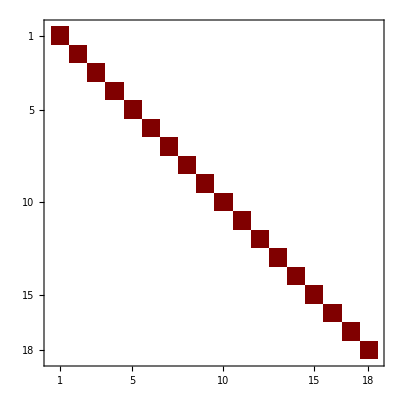

Diagonalized pseudo-scalar CP even mass form (π^1, π^3, K^1, K^3, η, η')

{-θ/u,-θ/u,-θ/u,-θ/u,-θ/u,-θ/u+3 u Λ3}

Diagonalized scalar CP even mass form (a^1, a^3, H^1, H^3, f, σ)

{-θ/u+2 u Λ3+2 u^2 λ_2,-θ/u+2 u Λ3+2 u^2 λ_2,-θ/u+2 u Λ3+2 u^2 λ_2,-θ/u+2 u Λ3+2 u^2 λ_2,-θ/u+2 u Λ3+2 u^2 λ_2,-θ/u-u Λ3+2 u^2 λ_1+2 u^2 λ_2}

Diagonalized pseudo-scalar CP odd mass form (π^2, K^2, K^4)

{-θ/u,-θ/u,-θ/u}

Diagonalized pseudo-scalar CP odd mass form (a^2, H^2, H^4)

{-θ/u+2 u Λ3+2 u^2 λ_2,-θ/u+2 u Λ3+2 u^2 λ_2,-θ/u+2 u Λ3+2 u^2 λ_2}

```mathematica
(*$Assumptions={u>0,v>0, {Λ3, Subscript[λ, 2], Subscript[λ, 1]} ∈ Reals, u>v};*)

(* Hessian *)
DDVGauge[i_,j_] := D[D[VGauge, SGauge[[i]]], SGauge[[j]]]/.SvacCGauge
MassFormGauge=Table[DDVGauge[i,j],{i,1,Length[SGauge]},{j,1,Length[SGauge]}];
Print["Mass form (after EWSB in Gauge states) block diagonal -> need to transform to mass basis. Will do this seperately for (pseudo-)scalar CP even/odd blocks"]
MatrixPlot[MassFormGauge]
MassFormGauge //MatrixForm;

(* Pseudo-scalar CP even *)
MassFormPSE=Table[DDVGauge[i,j],{i,1,6},{j,1,6}];
%//MatrixForm;
Print["Diagonalized pseudo-scalar CP even mass form (π^1, π^3, K^1, K^3, η, η')"]
MassPSE = Simplify[ToRadicals[Eigenvalues[MassFormPSE]]/.TadSolMu(*/.TadSolTheta/.TadSolLam3*) ]

(* Scalar CP even *)
MassFormSE=Table[DDVGauge[i,j],{i,7,12},{j,7,12}];
%//MatrixForm;
Print["Diagonalized scalar CP even mass form (a^1, a^3, H^1, H^3, f, σ)"]
MassSE = Simplify[ToRadicals[Eigenvalues[MassFormSE]]/.TadSolMu (*/.TadSolTheta/.TadSolLam3*) ]

(* Pseudo-scalar CP odd *)
MassFormPSO=Table[DDVGauge[i,j],{i,13,15},{j,13,15}];
%//MatrixForm;
Print["Diagonalized pseudo-scalar CP odd mass form (π^2, K^2, K^4)"]
MassPSO = Simplify[ToRadicals[Eigenvalues[MassFormPSO]]/.TadSolMu(*/.TadSolTheta/.TadSolLam3*) ]

(* Scalar CP odd *)
MassFormSO=Table[DDVGauge[i,j],{i,16,18},{j,16,18}];
%//MatrixForm;
Print["Diagonalized pseudo-scalar CP odd mass form (a^2, H^2, H^4)"]
MassSO = Simplify[ToRadicals[Eigenvalues[MassFormSO]]/.TadSolMu(*/.TadSolTheta/.TadSolLam3*) ]
```

### 2.5 Vacuum potential plot (IGNORE)

```mathematica
u=10000; Subscript[λ, 1]=-0.1; Subscript[λ, 2]=-0.1; Λ3=500;

f[ϕ_] = Simplify[(VGauge/.SvacGauge/.TadSolTheta /.TadSolMu/.v->ϕ)]
Plot[f[ϕ],{ϕ,-300,300}]



u=.;Subscript[λ, 1]=.; Subscript[λ, 2]=.; Λ3=.;μ2=.;θ=.;
```

ReplaceAll::reps: {SvacGauge} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {TadSolTheta} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SvacGauge} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(0.+0. ⅈ)-0.0625 a1^4-0.0625 a2^4+1.25×10^7 a3^2-0.0625 a3^4-353.553 a3^2 f+1.25×10^7 f^2-0.125 a3^2 f^2+117.851 f^3-0.0625 f^4+1.25×10^7 H1^2-306.186 a3 H1^2-0.125 a3^2 H1^2+176.777 f H1^2-0.125 f^2 H1^2-0.0625 H1^4+1.25×10^7 H2^2-306.186 a3 H2^2-0.125 a3^2 H2^2+176.777 f H2^2-0.125 f^2 H2^2-0.125 H1^2 H2^2-0.0625 H2^4+1.25×10^7 H3^2+306.186 a3 H3^2-0.125 a3^2 H3^2+176.777 f H3^2-0.125 f^2 H3^2-0.125 H1^2 H3^2-0.125 H2^2 H3^2-0.0625 H3^4+1.25×10^7 H4^2+306.186 a3 H4^2-0.125 a3^2 H4^2+176.777 f H4^2-0.125 f^2 H4^2-0.125 H1^2 H4^2-0.125 H2^2 H4^2-0.125 H3^2 H4^2-0.0625 H4^4+1.25×10^7 K1^2+306.186 a3 K1^2-0.125 a3^2 K1^2-176.777 f K1^2-0.173205 a3 f K1^2-0.225 f^2 K1^2-0.125 H1^2 K1^2-0.275 H2^2 K1^2-0.125 H3^2 K1^2-0.125 H4^2 K1^2-0.0625 K1^4+0.3 H1 H2 K1 K2+1.25×10^7 K2^2+306.186 a3 K2^2-0.125 a3^2 K2^2-176.777 f K2^2-0.173205 a3 f K2^2-0.225 f^2 K2^2-0.275 H1^2 K2^2-0.125 H2^2 K2^2-0.125 H3^2 K2^2-0.125 H4^2 K2^2-0.125 K1^2 K2^2-0.0625 K2^4-0.3 H2 H4 K1 K3+0.3 H1 H4 K2 K3+1.25×10^7 K3^2-306.186 a3 K3^2-0.125 a3^2 K3^2-176.777 f K3^2+0.173205 a3 f K3^2-0.225 f^2 K3^2-0.125 H1^2 K3^2-0.125 H2^2 K3^2-0.125 H3^2 K3^2-0.275 H4^2 K3^2-0.125 K1^2 K3^2-0.125 K2^2 K3^2-0.0625 K3^4+0.3 H2 H3 K1 K4-0.3 H1 H3 K2 K4+0.3 H3 H4 K3 K4+1.25×10^7 K4^2-306.186 a3 K4^2-0.125 a3^2 K4^2-176.777 f K4^2+0.173205 a3 f K4^2-0.225 f^2 K4^2-0.125 H1^2 K4^2-0.125 H2^2 K4^2-0.275 H3^2 K4^2-0.125 H4^2 K4^2-0.125 K1^2 K4^2-0.125 K2^2 K4^2-0.125 K3^2 K4^2-0.0625 K4^4-353.553 H1 K1 η+0.173205 a3 H1 K1 η+0.2 f H1 K1 η-353.553 H2 K2 η+0.173205 a3 H2 K2 η+0.2 f H2 K2 η-353.553 H3 K3 η-0.173205 a3 H3 K3 η+0.2 f H3 K3 η-353.553 H4 K4 η-0.173205 a3 H4 K4 η+0.2 f H4 K4 η+1.25×10^7 η^2-0.075 a3^2 η^2-353.553 f η^2-0.125 f^2 η^2-0.225 H1^2 η^2-0.225 H2^2 η^2-0.225 H3^2 η^2-0.225 H4^2 η^2-0.125 K1^2 η^2-0.125 K2^2 η^2-0.125 K3^2 η^2-0.125 K4^2 η^2-0.0625 η^4-500. H1 K1 ηp-0.122474 a3 H1 K1 ηp+0.0707107 f H1 K1 ηp-500. H2 K2 ηp-0.122474 a3 H2 K2 ηp+0.0707107 f H2 K2 ηp-500. H3 K3 ηp+0.122474 a3 H3 K3 ηp+0.0707107 f H3 K3 ηp-500. H4 K4 ηp+0.122474 a3 H4 K4 ηp+0.0707107 f H4 K4 ηp-0.0707107 a3^2 η ηp-500. f η ηp+0.0707107 f^2 η ηp+0.0353553 H1^2 η ηp+0.0353553 H2^2 η ηp+0.0353553 H3^2 η ηp+0.0353553 H4^2 η ηp+0.106066 K1^2 η ηp+0.106066 K2^2 η ηp+0.106066 K3^2 η ηp+0.106066 K4^2 η ηp+0.0707107 η^3 ηp+1.25×10^7 ηp^2-0.1 a3^2 ηp^2-0.1 f^2 ηp^2-0.1 H1^2 ηp^2-0.1 H2^2 ηp^2-0.1 H3^2 ηp^2-0.1 H4^2 ηp^2-0.2 K1^2 ηp^2-0.2 K2^2 ηp^2-0.2 K3^2 ηp^2-0.2 K4^2 ηp^2-0.2 η^2 ηp^2-0.05 ηp^4-0.00005 a3^2 θ-0.00005 f^2 θ-0.00005 H1^2 θ-0.00005 H2^2 θ-0.00005 H3^2 θ-0.00005 H4^2 θ-0.00005 K1^2 θ-0.00005 K2^2 θ-0.00005 K3^2 θ-0.00005 K4^2 θ-0.00005 η^2 θ-0.00005 ηp^2 θ+612.372 H3 K1 π1+0.3 a3 H3 K1 π1+0.173205 f H3 K1 π1+612.372 H4 K2 π1+0.3 a3 H4 K2 π1+0.173205 f H4 K2 π1+612.372 H1 K3 π1-0.3 a3 H1 K3 π1+0.173205 f H1 K3 π1+612.372 H2 K4 π1-0.3 a3 H2 K4 π1+0.173205 f H2 K4 π1-0.34641 H1 H3 η π1-0.34641 H2 H4 η π1-0.122474 H1 H3 ηp π1-0.122474 H2 H4 ηp π1-0.367423 K1 K3 ηp π1-0.367423 K2 K4 ηp π1+1.25×10^7 π1^2-0.275 a3^2 π1^2+353.553 f π1^2-0.075 f^2 π1^2-0.125 H1^2 π1^2-0.125 H2^2 π1^2-0.125 H3^2 π1^2-0.125 H4^2 π1^2-0.125 K1^2 π1^2-0.125 K2^2 π1^2-0.125 K3^2 π1^2-0.125 K4^2 π1^2-0.125 η^2 π1^2-0.212132 η ηp π1^2-0.2 ηp^2 π1^2-0.00005 θ π1^2-0.0625 π1^4-612.372 H4 K1 π2-0.3 a3 H4 K1 π2-0.173205 f H4 K1 π2+612.372 H3 K2 π2+0.3 a3 H3 K2 π2+0.173205 f H3 K2 π2+612.372 H2 K3 π2-0.3 a3 H2 K3 π2+0.173205 f H2 K3 π2-612.372 H1 K4 π2+0.3 a3 H1 K4 π2-0.173205 f H1 K4 π2-0.34641 H2 H3 η π2+0.34641 H1 H4 η π2-0.122474 H2 H3 ηp π2+0.122474 H1 H4 ηp π2-0.367423 K2 K3 ηp π2+0.367423 K1 K4 ηp π2+1.25×10^7 π2^2-0.275 a3^2 π2^2+353.553 f π2^2-0.075 f^2 π2^2-0.125 H1^2 π2^2-0.125 H2^2 π2^2-0.125 H3^2 π2^2-0.125 H4^2 π2^2-0.125 K1^2 π2^2-0.125 K2^2 π2^2-0.125 K3^2 π2^2-0.125 K4^2 π2^2-0.125 η^2 π2^2-0.212132 η ηp π2^2-0.2 ηp^2 π2^2-0.00005 θ π2^2-0.125 π1^2 π2^2-0.0625 π2^4+612.372 H1 K1 π3+0.173205 f H1 K1 π3+612.372 H2 K2 π3+0.173205 f H2 K2 π3-612.372 H3 K3 π3-0.173205 f H3 K3 π3-612.372 H4 K4 π3-0.173205 f H4 K4 π3+707.107 a3 η π3-0.1 a3 f η π3-0.173205 H1^2 η π3-0.173205 H2^2 η π3+0.173205 H3^2 η π3+0.173205 H4^2 η π3-500. a3 ηp π3-0.141421 a3 f ηp π3-0.0612372 H1^2 ηp π3-0.0612372 H2^2 ηp π3+0.0612372 H3^2 ηp π3+0.0612372 H4^2 ηp π3-0.183712 K1^2 ηp π3-0.183712 K2^2 ηp π3+0.183712 K3^2 ηp π3+0.183712 K4^2 ηp π3+1.25×10^7 π3^2-0.125 a3^2 π3^2+353.553 f π3^2-0.075 f^2 π3^2-0.125 H1^2 π3^2-0.125 H2^2 π3^2-0.125 H3^2 π3^2-0.125 H4^2 π3^2-0.125 K1^2 π3^2-0.125 K2^2 π3^2-0.125 K3^2 π3^2-0.125 K4^2 π3^2-0.125 η^2 π3^2-0.212132 η ηp π3^2-0.2 ηp^2 π3^2-0.00005 θ π3^2-0.125 π1^2 π3^2-0.125 π2^2 π3^2-0.0625 π3^4+250. a3^2 σ-0.212132 a3^2 f σ+250. f^2 σ+0.0707107 f^3 σ+250. H1^2 σ-0.183712 a3 H1^2 σ+0.106066 f H1^2 σ+250. H2^2 σ-0.183712 a3 H2^2 σ+0.106066 f H2^2 σ+250. H3^2 σ+0.183712 a3 H3^2 σ+0.106066 f H3^2 σ+250. H4^2 σ+0.183712 a3 H4^2 σ+0.106066 f H4^2 σ-250. K1^2 σ-0.0612372 a3 K1^2 σ+0.0353553 f K1^2 σ-250. K2^2 σ-0.0612372 a3 K2^2 σ+0.0353553 f K2^2 σ-250. K3^2 σ+0.0612372 a3 K3^2 σ+0.0353553 f K3^2 σ-250. K4^2 σ+0.0612372 a3 K4^2 σ+0.0353553 f K4^2 σ+0.0707107 H1 K1 η σ+0.0707107 H2 K2 η σ+0.0707107 H3 K3 η σ+0.0707107 H4 K4 η σ-250. η^2 σ+0.0707107 f η^2 σ-0.2 H1 K1 ηp σ-0.2 H2 K2 ηp σ-0.2 H3 K3 ηp σ-0.2 H4 K4 ηp σ-0.2 f η ηp σ+500. ηp^2 σ+1. θ σ-0.122474 H3 K1 π1 σ-0.122474 H4 K2 π1 σ-0.122474 H1 K3 π1 σ-0.122474 H2 K4 π1 σ-250. π1^2 σ-0.0707107 f π1^2 σ+0.122474 H4 K1 π2 σ-0.122474 H3 K2 π2 σ-0.122474 H2 K3 π2 σ+0.122474 H1 K4 π2 σ-250. π2^2 σ-0.0707107 f π2^2 σ-0.122474 H1 K1 π3 σ-0.122474 H2 K2 π3 σ+0.122474 H3 K3 π3 σ+0.122474 H4 K4 π3 σ-0.141421 a3 η π3 σ-0.2 a3 ηp π3 σ-250. π3^2 σ-0.0707107 f π3^2 σ+1.25×10^7 σ^2-0.2 a3^2 σ^2-0.2 f^2 σ^2-0.2 H1^2 σ^2-0.2 H2^2 σ^2-0.2 H3^2 σ^2-0.2 H4^2 σ^2-0.1 K1^2 σ^2-0.1 K2^2 σ^2-0.1 K3^2 σ^2-0.1 K4^2 σ^2-0.1 η^2 σ^2-0.1 ηp^2 σ^2-0.00005 θ σ^2-0.1 π1^2 σ^2-0.1 π2^2 σ^2-0.1 π3^2 σ^2-166.667 σ^3-0.05 σ^4+a2^2 (1.25×10^7-0.125 a3^2-0.125 f^2-0.125 H1^2-0.125 H2^2-0.125 H3^2-0.125 H4^2-0.125 K1^2-0.125 K2^2-0.125 K3^2-0.125 K4^2-0.075 η^2-0.0707107 η ηp-0.1 ηp^2-0.00005 θ-0.275 π1^2-0.125 π2^2-0.275 π3^2+f (-353.553-0.212132 σ)+250. σ-0.2 σ^2)+a1^2 (1.25×10^7-0.125 a2^2-0.125 a3^2-353.553 f-0.125 f^2-0.125 H1^2-0.125 H2^2-0.125 H3^2-0.125 H4^2-0.125 K1^2-0.125 K2^2-0.125 K3^2-0.125 K4^2-0.075 η^2-0.0707107 η ηp-0.1 ηp^2-0.00005 θ-0.125 π1^2-0.275 π2^2-0.275 π3^2+250. σ-0.212132 f σ-0.2 σ^2)+a1 (612.372 K1 K3-0.34641 f K1 K3+612.372 K2 K4-0.34641 f K2 K4+0.173205 H3 K1 η+0.173205 H4 K2 η-0.122474 H3 K1 ηp-0.122474 H4 K2 ηp+707.107 η π1-0.1 f η π1-500. ηp π1-0.141421 f ηp π1-0.3 H4 K3 π2+0.3 H3 K4 π2+0.3 a2 π1 π2-0.3 H3 K1 π3-0.3 H4 K2 π3+0.3 a3 π1 π3+H1 (0.173205 K3 η-0.122474 K3 ηp-0.3 K2 π2+0.3 K3 π3+H3 (-612.372-0.367423 σ))-0.122474 K1 K3 σ-0.122474 K2 K4 σ-0.141421 η π1 σ-0.2 ηp π1 σ+H2 (-612.372 H4+0.173205 K4 η-0.122474 K4 ηp+0.3 K1 π2+0.3 K4 π3-0.367423 H4 σ))+a2 (612.372 K2 K3-0.34641 f K2 K3-612.372 K1 K4+0.34641 f K1 K4-0.173205 H4 K1 η+0.173205 H3 K2 η+0.122474 H4 K1 ηp-0.122474 H3 K2 ηp+0.3 H4 K3 π1-0.3 H3 K4 π1+707.107 η π2-0.1 f η π2-500. ηp π2-0.141421 f ηp π2+0.3 H4 K1 π3-0.3 H3 K2 π3+0.3 a3 π2 π3+H2 (0.173205 K3 η-0.122474 K3 ηp-0.3 K1 π1+0.3 K3 π3+H3 (-612.372-0.367423 σ))-0.122474 K2 K3 σ+0.122474 K1 K4 σ-0.141421 η π2 σ-0.2 ηp π2 σ+H1 (612.372 H4-0.173205 K4 η+0.122474 K4 ηp+0.3 K2 π1-0.3 K4 π3+0.367423 H4 σ))/.SvacGauge/.TadSolTheta

-Graphics-

## 3. Breaking Chiral and EW Symmetries (High-scale model, Complex weak basis)

### 3.1 Chiral tadpole equations

```mathematica
(* Potential explcitly in terms of gauge eigenstates *)
VvacC=Expand[Simplify[V/.SvacC]]

(* === Same tadpole equations as in section 2.1 (gauge basis) === *)
Print["Solutions for μ2 from tadpole equations"]
TadSolMu
(*TadSolOmega*)
```

u θ-(u^3 Λ3)/3-(u^2 μ2)/2+(u^4 λ_1)/4+(u^4 λ_2)/4

Solutions for μ2 from tadpole equations

TadSolMu

### 3.2 Chiral Symmetry breaking MassForms

```mathematica
(* Hessian *)
DDV[i_,j_] := D[D[V, S[[i]]], Sc[[j]]]
MassFormEW=Table[DDV[i,j],{i,1,Length[S]},{j,1,Length[Sc]}]/.SvacC;
Print["Mass form (after EWSB in charged basis) block diagonal -> need to transform to mass basis. Will do this seperately for (pseudo-)scalar CP even/odd blocks"]
MatrixPlot[MassFormEW]
MassFormEW //MatrixForm;


(* Pseudo-scalar T-mesons *)
MassFormPSM=Table[DDV[i,j],{i,1,8},{j,1,8}]/.SvacC /.TadSolMu;
%//MatrixForm
Print["Diagonalized pseudo-scalar T-mesons mass form"]
Simplify[Eigenvalues[MassFormPSM](*/.TadSolTheta/.TadSolLam3*) ]

(* Pseudo-scalar T-glueball *)
MassFormPSG=Table[DDV[i,j],{i,9,9},{j,9,9}]/.SvacC/.TadSolMu;
%//MatrixForm;
Print["Diagonalized Pseudo-scalar T-glueball mass form"]
Simplify[Eigenvalues[MassFormPSG] (*/.TadSolTheta/.TadSolLam3*) ]

(* Scalar T-mesons *)
MassFormSM=Table[DDV[i,j],{i,10,17},{j,10,17}]/.SvacC/.TadSolMu;
%//MatrixForm;
Print["Diagonalized Scalar T-mesons mass form "]
Simplify[Eigenvalues[MassFormSM](*/.TadSolTheta/.TadSolLam3*) ]

(* Scalar T-glueball *)
MassFormSG=Table[DDV[i,j],{i,18,18},{j,18,18}]/.SvacC/.TadSolMu;
%//MatrixForm;
Print["Diagonalized Scalar T-glueball mass form "]
Simplify[Eigenvalues[MassFormSG](*/.TadSolTheta/.TadSolLam3*) ]

Mass = {MassFormPSM[[1,1]]==MassPSM, MassFormPSG[[1,1]]==MassPSG, MassFormSM[[1,1]]==MassSM, MassFormSG[[1,1]]==MassSG} //Simplify;
Print["This is the inversion procedure"]
MassSolve = NSolve[Mass,{θ,Λ3,Subscript[λ, 2],Subscript[λ, 1] }]
```

Mass form (after EWSB in charged basis) block diagonal -> need to transform to mass basis. Will do this seperately for (pseudo-)scalar CP even/odd blocks

-Graphics-

ReplaceAll::reps: {TadSolMu} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0,0,0,0,0},{0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0,0,0,0},{0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0,0,0},{0,0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0,0},{0,0,0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0},{0,0,0,0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0},{0,0,0,0,0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0},{0,0,0,0,0,0,0,-u Λ3-μ2+2 u^2 (λ_1/2+λ_2/2)}}/.TadSolMu

Diagonalized pseudo-scalar T-mesons mass form

Eigenvalues[{{-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0,0,0,0,0},{0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0,0,0,0},{0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0,0,0},{0,0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0,0},{0,0,0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0,0},{0,0,0,0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0,0},{0,0,0,0,0,0,-u Λ3-μ2+u^2 (λ_1+λ_2),0},{0,0,0,0,0,0,0,-u Λ3-μ2+u^2 λ_1+u^2 λ_2}}/.TadSolMu]

ReplaceAll::reps: {TadSolMu} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Diagonalized Pseudo-scalar T-glueball mass form

Eigenvalues[{{2 u Λ3-μ2+u^2 λ_1+u^2 λ_2}}/.TadSolMu]

ReplaceAll::reps: {TadSolMu} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Diagonalized Scalar T-mesons mass form

Eigenvalues[{{u Λ3-μ2+u^2 (λ_1+3 λ_2),0,0,0,0,0,0,0},{0,u Λ3-μ2+u^2 (λ_1+3 λ_2),0,0,0,0,0,0},{0,0,u Λ3-μ2+u^2 (λ_1+3 λ_2),0,0,0,0,0},{0,0,0,u Λ3-μ2+u^2 (λ_1+3 λ_2),0,0,0,0},{0,0,0,0,u Λ3-μ2+u^2 (λ_1+3 λ_2),0,0,0},{0,0,0,0,0,u Λ3-μ2+u^2 (λ_1+3 λ_2),0,0},{0,0,0,0,0,0,u Λ3-μ2+u^2 (λ_1+3 λ_2),0},{0,0,0,0,0,0,0,u Λ3-μ2+u^2 λ_1+3 u^2 λ_2}}/.TadSolMu]

ReplaceAll::reps: {TadSolMu} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Diagonalized Scalar T-glueball mass form

Eigenvalues[{{-2 u Λ3-μ2+3 u^2 λ_1+3 u^2 λ_2}}/.TadSolMu]

This is the inversion procedure

{}

### 3.3 EW tadpole equations

```mathematica
Print["Vacuum potential"]
VvacEW=Expand[Simplify[(VEW/.EW2Gauge)/.SvacEWGauge]] [[1,1]]

DVGauge2[i_] := D[(VEW/.EW2Gauge)[[1,1]], SGauge[[i]]];
Print["Tadpole equations"]
TadpolesEW =Table[(DVGauge2[i]),{i,1,Length[SGauge]}] /.SvacEWGauge //Simplify


TadpoleEW = Simplify[{(DVGauge2[8]/.SvacEWGauge) ==0, (DVGauge2[10]/.SvacEWGauge) ==0,(DVGauge2[11]/.SvacEWGauge) ==0,(DVGauge2[12]/.SvacEWGauge) ==0}];
Print["Tadpole solutions"]
TadSolEW = Solve[TadpoleEW,{Γ222,mH22,mS34,mS44}][[1]]


(*Print["Extreemum = minimum requirment"]
D[D[VGauge/.SvacCGauge, u],u] /.TadSolMu //Simplify*)
```

Vacuum potential

-mS44 u^2+(mH22 v^2)/2+u^3 α444+1/2 u v^2 γ422+u^4 Δ4444+u θ+1/2 u^2 v^2 Π4422+(v^4 υ22)/4

Tadpole equations

{0,0,0,0,0,0,0,-(v^2 (Γ222+u Ζ4222))/(2 √2),0,v (mH22+u γ422+u^2 Π4422+v^2 υ22),1/2 (-2 mS34 u+2 u^2 α344+v^2 γ322+2 u^3 Δ3444+u v^2 Π3422),-2 mS44 u+3 u^2 α444+(v^2 γ422)/2+4 u^3 Δ4444+θ+u v^2 Π4422,0,0,0,0,0,0}

Tadpole solutions

{Γ222→-u Ζ4222,mH22→-u γ422-u^2 Π4422-v^2 υ22,mS34→(2 u^2 α344+v^2 γ322+2 u^3 Δ3444+u v^2 Π3422)/(2 u),mS44→(6 u^2 α444+v^2 γ422+8 u^3 Δ4444+2 θ+2 u v^2 Π4422)/(4 u)}

Full mass form

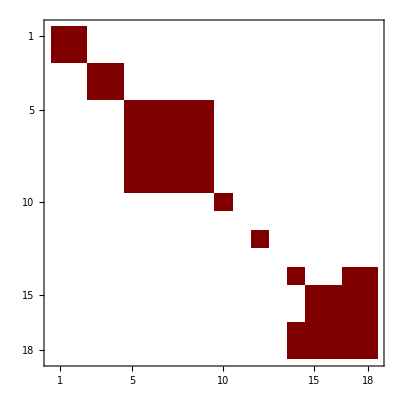

Charged particles. Note one Goldstone boson

(-2 mT11+2 u β411+2 u^2 η4411+(v^2 τ7)/2 | (v Γ112)/(√2)+(u v Ζ4112)/(√2)
(v Γ211)/(√2)+(u v Ζ4211)/(√2) | mH11+u γ411+u^2 Π4411+(v^2 ψ1)/2)

(1/4 (2 mH11-4 mT11+4 u β411+2 u γ411+4 u^2 η4411+2 u^2 Π4411+v^2 τ7+v^2 ψ1-√(-4 (8 u (-mT11+u (β411+u η4411)) (γ411+u Π4411)+mH11 (-8 mT11+8 u (β411+u η4411)+2 v^2 τ7)+2 v^2 (-((Γ112+u Ζ4112) (Γ211+u Ζ4211))+u (γ411+u Π4411) τ7)+v^2 (-4 mT11+4 u (β411+u η4411)+v^2 τ7) ψ1)+(2 mH11-4 mT11+2 u (2 β411+γ411+2 u η4411+u Π4411)+v^2 (τ7+ψ1))^2)) | 0
0 | 1/4 (2 mH11-4 mT11+4 u β411+2 u γ411+4 u^2 η4411+2 u^2 Π4411+v^2 τ7+v^2 ψ1+√(-4 (8 u (-mT11+u (β411+u η4411)) (γ411+u Π4411)+mH11 (-8 mT11+8 u (β411+u η4411)+2 v^2 τ7)+2 v^2 (-((Γ112+u Ζ4112) (Γ211+u Ζ4211))+u (γ411+u Π4411) τ7)+v^2 (-4 mT11+4 u (β411+u η4411)+v^2 τ7) ψ1)+(2 mH11-4 mT11+2 u (2 β411+γ411+2 u η4411+u Π4411)+v^2 (τ7+ψ1))^2)))

```mathematica
Print["Full mass form"]
DDVEW[i_,j_] := D[D[VEW, S[[i]]], Sc[[j]]][[1,1]]
MassFormEW=Table[DDVEW[i,j],{i,1,Length[S]},{j,1,Length[Sc]}]/.SvacEW /.TadSolEW;
MatrixPlot[MassFormEW]

Print["Charged particles. Note one Goldstone boson"]
MassFormPSC = Table[DDVEW[i,j],{i,1,2},{j,1,2}]/.SvacEW /.TadSolEW;
%//MatrixForm
DiagMassFormPSC = DiagonalMatrix[FullSimplify[Eigenvalues[MassFormPSC]]];
%//MatrixForm
(*
Print["Neutral particles. Need to diagonalize!"]
MassFormLSN = Table[DDVLS[i,j],{i,5,8},{j,5,8}]/.SvacEW /.TadSolLS;
%//MatrixForm
Print["Neutral particles. Diagonalized. Note one Goldstone boson"]
DiagMassFormLSN = DiagonalMatrix[FullSimplify[Eigenvalues[MassFormLSN]]];
%//MatrixForm

MassLS = {MassFormLSC[[1,1]]==mC, DiagMassFormLSN[[2,2]]==mH, DiagMassFormLSN[[3,3]]==mN1, DiagMassFormLSN[[4,4]]==mN2};
Print["This is the inversion procedure"]
MassSolveLS = Solve[MassLS,{L9, mT, mS,L8 }][[1]]


NumInParamC = {L10->0.1, v->246, L7 ->0.1, mH->125, mC->300, mN1->400, mN2->200};

Print["Testing inversion. Charged particles"]
MassFormLSC/.MassSolveLS/.NumInParamC;
%//MatrixForm

Print["Testing inversion. Neutral particles"]
DiagMassFormLSN/.MassSolveLS/.NumInParamC;
%//MatrixForm
*)
```

## 4. Light Model

### 4.1 Potential

```mathematica
(* === States === *)
Sheavy={πp->0,π0->0,πm->0,Kp->0,K0->0,Km->0,Kb0->0,η->0,ηp->0,σ->0};

SLS= {ap,Hp,am,Hm,a0,H0,Hb0,f};
ScLS = {am,Hm,ap,Hp,a0,Hb0,H0,f};
SLSGauge = {a1,a2,a3,f,H3,H1,H2,H4};

STripGauge = {a1,a2,a3,H3,H1,H2,H4};

SvacEW={πp->0, π0->0, πm->0, Kp->0, K0->0, Kb0->0, Km->0, η->0, ηp->0, ap->0, a0->0, am->0, Hp->0, H0->v/Sqrt[2], Hb0->v/Sqrt[2], Hm->0, f->0, σ->u} ;
SvacEWGauge={π1->0,π3->0,K1->0,K3->0,η->0,ηp->0,a1->0,a3->0,H1->0,H3->v,f->0,σ->u,π2->0,K2->0,K4->0, a2->0,H2->0,H4->0};


VLS = (mS Sing[[3]]^2+ mu2 Hc.H + mT Tr[a.a]
		+L1 Sing[[3]]^3+ L2 Sing[[3]]Tr[a.a] + L3 Sing[[3]]Hc.H+ L4 Hc.a.H 
		+ L5 Sing[[3]]^4+L6 Sing[[3]]^2 Tr[a.a] + L7 Sing[[3]]^2 Hc.H+L8 Sing[[3]]Hc.a.H + L9 (Hc.H)^2 + L10 Hc.a.a.H  + L11 Tr[a.a.a.a]  )[[1,1]];
VLSGauge = VLS /.EW2Gauge;


VTrip = (mu2T Hc.H + mTT Tr[a.a]+ LT1 Hc.a.H + LT2 (Hc.H)^2 + LT3 Hc.a.a.H  + LT4 Tr[a.a.a.a]  )[[1,1]];
VTripGauge = VTrip /.EW2Gauge;
```

### 4.2 Vacuum potential and tadpole equations

```mathematica
Print["Low-scale vaccum potential"]
VvacLS= Expand[Simplify[VLSGauge/.SvacEWGauge]]

DVLS[i_]:=D[VLSGauge,SLSGauge[[i]]];
Print["Tadpole equations"]
Table[(DVLS[i]/.SvacEWGauge),{i,1,Length[SLS]}]
TadpoleLS=Simplify[{(DVLS[3]/.SvacEWGauge)==0,(DVLS[4]/.SvacEWGauge)==0,(DVLS[5]/.SvacEWGauge)==0}];
Print["Tadpole solutions"]
TadSolLS = Solve[TadpoleLS,{L4,L3, mu2}][[1]]


Print["Trip vaccum potential"]
VvacTrip= Expand[Simplify[VTripGauge/.SvacEWGauge]]

DVTrip[i_]:=D[VTripGauge,STripGauge[[i]]];
Print["Trip Tadpole equations"]
Table[(DVTrip[i]/.SvacEWGauge),{i,1,Length[STripGauge]}]
(*TadpoleLS=Simplify[{(DVLS[3]/.SvacEWGauge)==0,(DVLS[4]/.SvacEWGauge)==0,(DVLS[5]/.SvacEWGauge)==0}];
Print["Tadpole solutions"]
TadSolLS = Solve[TadpoleLS,{L4,L3, mu2}][[1]]*)
```

Low-scale vaccum potential

(mu2 v^2)/2+(L9 v^4)/4

Tadpole equations

{0,0,-(L4 v^2)/(2 √2),(L3 v^2)/2,mu2 v+L9 v^3,0,0,0}

Tadpole solutions

{L4→0,L3→0,mu2→-L9 v^2}

Trip vaccum potential

(mu2T v^2)/2+(LT2 v^4)/4

Trip Tadpole equations

{0,0,-(LT1 v^2)/(2 √2),mu2T v+LT2 v^3,0,0,0}

### 4.3 MassForms, inversion (complex basis)

```mathematica
Print["Full mass form"]
DDVLS[i_,j_] := D[D[VLS, SLS[[i]]], ScLS[[j]]]
MassFormLS=Table[DDVLS[i,j],{i,1,Length[SLS]},{j,1,Length[ScLS]}]/.SvacEW /.TadSolLS;
%//MatrixForm

Print["Charged particles. Note one Goldstone boson"]
MassFormLSC = Table[DDVLS[i,j],{i,1,2},{j,1,2}]/.SvacEW /.TadSolLS;
%//MatrixForm

Print["Neutral particles. Need to diagonalize!"]
MassFormLSN = Table[DDVLS[i,j],{i,5,8},{j,5,8}]/.SvacEW /.TadSolLS;
%//MatrixForm
Print["Neutral particles. Diagonalized. Note one Goldstone boson"]
DiagMassFormLSN = DiagonalMatrix[FullSimplify[Eigenvalues[MassFormLSN]]];
%//MatrixForm

MassLS = {MassFormLSC[[1,1]]==mC, DiagMassFormLSN[[2,2]]==mH, DiagMassFormLSN[[3,3]]==mN1, DiagMassFormLSN[[4,4]]==mN2}
Print["This is the inversion procedure"]
MassSolveLS = Solve[MassLS,{L9, mT, mS,L8 }][[1]]


NumInParamC = {L10->0.1, v->246, L7 ->0.1, mH->125, mC->300, mN1->400, mN2->200};

Print["Testing inversion. Charged particles"]
MassFormLSC/.MassSolveLS/.NumInParamC;
%//MatrixForm

Print["Testing inversion. Neutral particles"]
DiagMassFormLSN/.MassSolveLS/.NumInParamC;
%//MatrixForm
```

Full mass form

(2 mT+(L10 v^2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 mT+(L10 v^2)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 mT+(L10 v^2)/2 | 0 | 0 | -(L8 v^2)/(2 √2)
0 | 0 | 0 | 0 | 0 | L9 v^2 | L9 v^2 | 0
0 | 0 | 0 | 0 | 0 | L9 v^2 | L9 v^2 | 0
0 | 0 | 0 | 0 | -(L8 v^2)/(2 √2) | 0 | 0 | 2 mS+L7 v^2)

Charged particles. Note one Goldstone boson

(2 mT+(L10 v^2)/2 | 0
0 | 0)

Neutral particles. Need to diagonalize!

(2 mT+(L10 v^2)/2 | 0 | 0 | -(L8 v^2)/(2 √2)
0 | L9 v^2 | L9 v^2 | 0
0 | L9 v^2 | L9 v^2 | 0
-(L8 v^2)/(2 √2) | 0 | 0 | 2 mS+L7 v^2)

Neutral particles. Diagonalized. Note one Goldstone boson

(0 | 0 | 0 | 0
0 | 2 L9 v^2 | 0 | 0
0 | 0 | mS+mT+1/4 ((L10+2 L7) v^2-√(16 (mS-mT)^2-8 (L10-2 L7) (mS-mT) v^2+((L10-2 L7)^2+2 L8^2) v^4)) | 0
0 | 0 | 0 | mS+1/4 (4 mT+(L10+2 L7) v^2+√(16 (mS-mT)^2-8 (L10-2 L7) (mS-mT) v^2+((L10-2 L7)^2+2 L8^2) v^4)))

{2 mT+(L10 v^2)/2==mC,2 L9 v^2==mH,mS+mT+1/4 ((L10+2 L7) v^2-√(16 (mS-mT)^2-8 (L10-2 L7) (mS-mT) v^2+((L10-2 L7)^2+2 L8^2) v^4))==mN1,mS+1/4 (4 mT+(L10+2 L7) v^2+√(16 (mS-mT)^2-8 (L10-2 L7) (mS-mT) v^2+((L10-2 L7)^2+2 L8^2) v^4))==mN2}

This is the inversion procedure

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{L9→mH/(2 v^2),mT→1/4 (2 mC-L10 v^2),mS→1/2 (-mC+mN1+mN2-L7 v^2),L8→-(2 ⅈ √2 √(mC-mN1) √(mC-mN2))/v^2}

Testing inversion. Charged particles

(300. | 0
0 | 0)

Testing inversion. Neutral particles

(0 | 0 | 0 | 0
0 | 125 | 0 | 0
0 | 0 | 200. | 0
0 | 0 | 0 | 400.)

### 4.4 Fnding SM Higgs boson mass (real basis)

```mathematica
Print["Full mass form. Note the 5th diagonal element, which is block diagonal and corresponds
to the H3 field. It becomes apparent here that 2L9v^2 is the mass for the SM Higgs boson!"]
DDVLS[i_,j_] := D[D[VLSGauge, SLSGauge[[i]]], SLSGauge[[j]]]
MassFormLS=Table[DDVLS[i,j],{i,1,Length[SLSGauge]},{j,1,Length[SLSGauge]}]/.SvacEWGauge/.TadSolLS;
%//MatrixForm
```

Full mass form. Note the 5th diagonal element, which is block diagonal and corresponds
to the H3 field. It becomes apparent here that 2L9v^2 is the mass for the SM Higgs boson!

(-2 mT+(L10 v^2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 mT+(L10 v^2)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 mT+(L10 v^2)/2 | -(L8 v^2)/(2 √2) | 0 | 0 | 0 | 0
0 | 0 | -(L8 v^2)/(2 √2) | -2 mS+L7 v^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 L9 v^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Extra

```mathematica
(Tr[a.a]* Tr[a.a] /.EW2Gauge) //Expand
(Tr[a.a.a.a] /.EW2Gauge) //Expand
```

a1^4+2 a1^2 a2^2+a2^4+2 a1^2 a3^2+2 a2^2 a3^2+a3^4

a1^4/2+a1^2 a2^2+a2^4/2+a1^2 a3^2+a2^2 a3^2+a3^4/2

### Useful for analysis

```mathematica
Coefficient[ChiralV4D,(am ap πm πp )];
Kc.H;
Expand[(a.a)^2];
Expand[ a.a.a.a];
Expand[Tr[ππ.a.ππ.a]];
Expand[Tr[ππ.ππ.a.a]];

Expand[Kc.H.Hc.K];

Simplify[(V-ChiralV)/.InputParam2D/.InputParam3D/.InputParam4D][[1,1]];

V /.InputParam2D/.InputParam3D/.InputParam4D;



STest={ap, a0, am, Hp, H0, Hb0, Hm} ;
ScTest={am, a0, ap, Hm, Hb0, H0, Hp} ;

VTest = (mT22 Tr[a.a]+ mH22 Hc.H+Γ222 Hc.a.H+τ8 Hc.a.a.H+Λ22 Tr[a.a.a.a]+υ22 (Hc.H)^2)[[1,1]];
VTest= %/.InputParam2D/.InputParam3D/.InputParam4D ;

DV[i_] := D[VTest, STest[[i]]];

(* Chiral Tadpole equation *)
TadpoleC = Simplify[DV[5] /. SvacEW] == 0;
TadSolMu2 = Solve[TadpoleC, μ2][[1,1]];
```

### Numerical mass (gauge basis)

```mathematica
(* Pick your parameters *)
u=10000; v=246; Subscript[λ, 1]=0.1; Subscript[λ, 2]=0.1; Λ3=500;
μ2=TadSolMu[[All,2]][[1]]; θ=TadSolTheta[[All,2]][[1]];


(* Pseudo-scalar CP even *)
MassFormPSE=Table[DDVGauge[i,j],{i,1,6},{j,1,6}];
Print["Diagonalized pseudo-scalar CP even mass form -> Masses for for π^1, π^3, K^1, K^3, η, η' "]
MassFormPSE = MassFormPSE ;  (* Insert model input parameters and VEVs *)
Round[Eigenvalues[MassFormPSE],0.01]

(* Scalar CP even *)
MassFormSE=Table[DDVGauge[i,j],{i,7,12},{j,7,12}];
Print["Diagonalized scalar CP even mass form -> Masses for for a^1, a^3, H^1, H^3, f, σ "]
MassFormSE = MassFormSE ; 
Round[Eigenvalues[MassFormSE],0.01]

(* Pseudo-scalar CP odd *)
MassFormPSO=Table[DDVGauge[i,j],{i,13,15},{j,13,15}];
Print["Diagonalized pseudo-scalar CP odd mass form -> Masses for for π^2, K^2, K^4 "]
MassFormPSO = MassFormPSO ;  
Round[Eigenvalues[MassFormPSO],0.01]

(* Scalar CP odd *)
MassFormSO=Table[DDVGauge[i,j],{i,16,18},{j,16,18}];
Print["Diagonalized pseudo-scalar CP odd mass form -> Masses for for a^2, H^2, H^4 "]
MassFormSO = MassFormSO ;  
Round[Eigenvalues[MassFormSO],0.01]


u=.;v=.;Subscript[λ, 1]=.; Subscript[λ, 2]=.; Λ3=.;μ2=.;θ=.;
```